```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

2963

2963

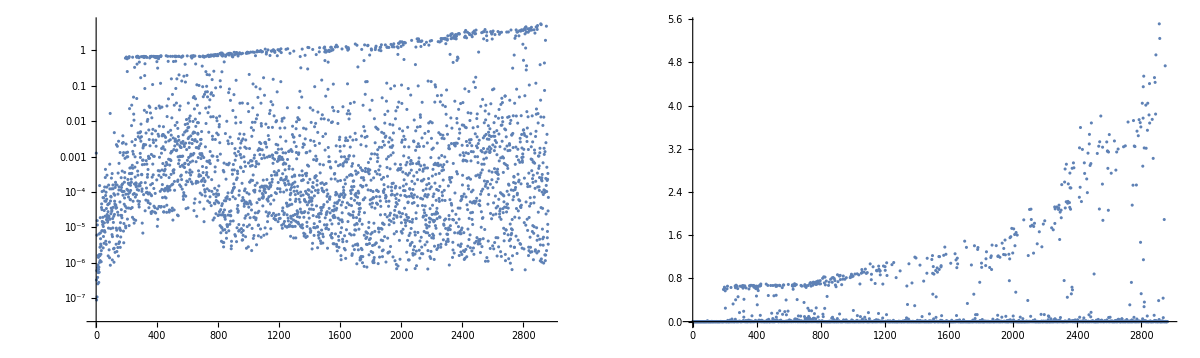

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

S1EL_xOffset : 0.0029704027
S1EL_yOffset : 0.000157488
S2EL_xOffset : 0.0006569286
S2EL_yOffset : 0.0023142176
S2ER_xOffset : -0.001198114
S2ER_yOffset : -0.0015461669
S1ER_xOffset : 0.0035274545
S1ER_yOffset : 0.0011987938
XC1FFkG : 0.4876890795
XC3FFkG : -0.2159115185
YC1FFkG : 0.007957465
YC2FFkG : -0.2105666363
PDrive_mean_x : -3.0189e-6
PDrive_mean_y : -6.6581e-6
PDrive_sigma_x : 0.0000538294
PDrive_sigma_y : 0.0000569317
PDrive_mean_xp : 0.0015079468
PDrive_mean_yp : -0.0008954822
PDrive_median_x : 1.2643e-6
PDrive_median_y : 3.0127e-6
PDrive_median_xp : 0.0016180089
PDrive_median_yp : -0.0008798563
PDrive_sigmaSI90_x : 0.0000465618
PDrive_sigmaSI90_y : 0.0000487328
PDrive_sigmaSI90_z : 0.0000244671
PDrive_emitSI90_x : 0.0001459483
PDrive_emitSI90_y : 0.0000290426
PDrive_zCentroid : 991.3317553195
PWitness_mean_x : -5.5109e-6
PWitness_mean_y : -6.5391e-6
PWitness_sigma_x : 0.0000344842
PWitness_sigma_y : 0.0000312065
PWitness_mean_xp : 0.0017936477
PWitness_mean_yp : -0.0010006814
PWitness_median_x : -4.4514e-6
PWitness_median_y : -4.79e-6
PWitness_median_xp : 0.0017998979
PWitness_median_yp : -0.0010024312
PWitness_sigmaSI90_x : 0.0000327884
PWitness_sigmaSI90_y : 0.0000287625
PWitness_sigmaSI90_z : 0.0000131485
PWitness_emitSI90_x : 0.0000341889
PWitness_emitSI90_y : 0.0000119122
PWitness_zCentroid : 991.3319060028
bunchSpacing : 0.0001506834
transverseCentroidOffset : 2.4948e-6
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 1.0882346094
maximizeMe : 5.5135169827

## Plot all

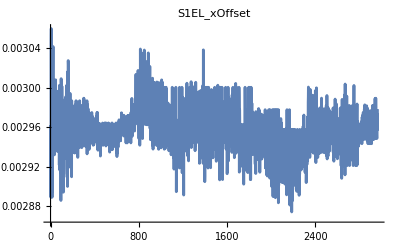
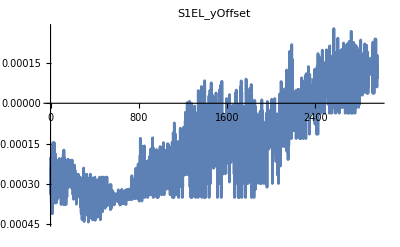
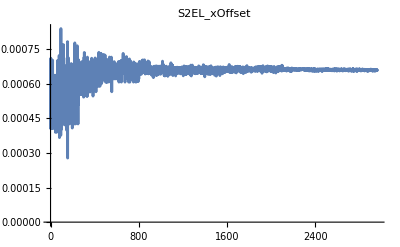
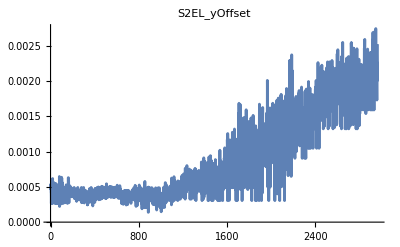
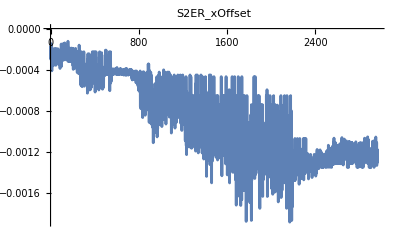
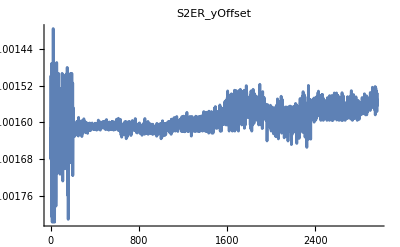
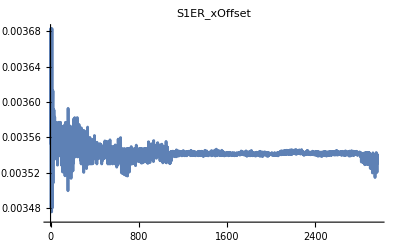
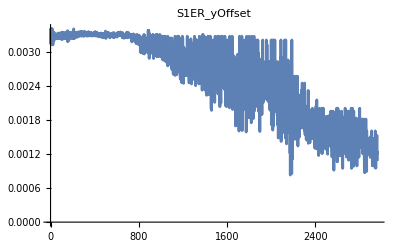
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_sigmaSI90_z"
(*fitVar = "bunchSpacing"*)
```

PDrive_sigmaSI90_z

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

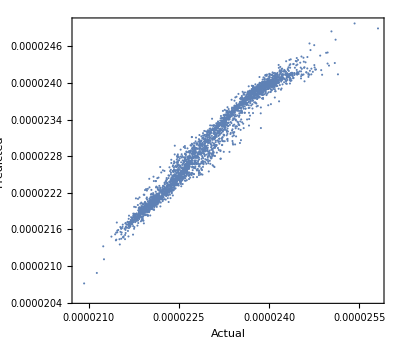

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

General::munfl: Exp[-980.959] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4773.78] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1390.67] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| DF | SS | MS | F-Statistic | P-Value
S1ELxOffset | 1 | 5.63325×10^-11 | 5.63325×10^-11 | 2771.59 | 0.
S1ELyOffset | 1 | 1.46127×10^-9 | 1.46127×10^-9 | 71895.1 | 0.
S1ERxOffset | 1 | 2.2304×10^-13 | 2.2304×10^-13 | 10.9737 | 0.000935306
S1ERyOffset | 1 | 9.35552×10^-11 | 9.35552×10^-11 | 4602.96 | 0.
S2ELxOffset | 1 | 2.56895×10^-11 | 2.56895×10^-11 | 1263.94 | 1.00153×10^-230
S2ELyOffset | 1 | 8.27154×10^-14 | 8.27154×10^-14 | 4.06963 | 0.0437511
S2ERxOffset | 1 | 1.95854×10^-10 | 1.95854×10^-10 | 9636.11 | 0.
S2ERyOffset | 1 | 3.5757×10^-13 | 3.5757×10^-13 | 17.5926 | 0.0000281715
XC1FFkG | 1 | 1.08522×10^-13 | 1.08522×10^-13 | 5.33934 | 0.020918
XC3FFkG | 1 | 4.71439×10^-13 | 4.71439×10^-13 | 23.195 | 1.5376×10^-6
YC1FFkG | 1 | 6.44024×10^-14 | 6.44024×10^-14 | 3.16863 | 0.0751684
YC2FFkG | 1 | 3.2846×10^-12 | 3.2846×10^-12 | 161.604 | 4.3873×10^-36
Error | 2950 | 5.99588×10^-11 | 2.0325×10^-14 |  | 
Total | 2962 | 1.89725×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.0029704 | 0.00258515
S1EL_yOffset | -0.000241114 | 0.000157488 | 0.000398602
S2EL_xOffset | -0.00141787 | 0.000656929 | 0.0020748
S2EL_yOffset | 0.0000111705 | 0.00231422 | 0.00230305
S2ER_xOffset | -0.00223816 | -0.00119811 | 0.00104005
S2ER_yOffset | -0.000675996 | -0.00154617 | -0.000870171
S1ER_xOffset | 0.00100714 | 0.00352745 | 0.00252032
S1ER_yOffset | 0.000398456 | 0.00119879 | 0.000800338
XC1FFkG | 0.206455 | 0.487689 | 0.281234
XC3FFkG | -0.0899164 | -0.215912 | -0.125995
YC1FFkG | -0.0022312 | 0.00795747 | 0.0101887
YC2FFkG | -0.00851158 | -0.210567 | -0.202055